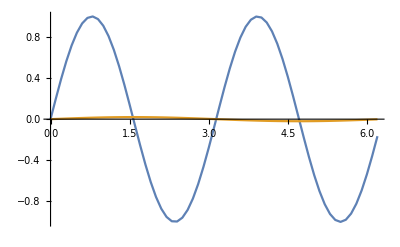

```mathematica
realData=Table[Sin[2 x],{x,0,2π,0.1}];
imData=Table[0.02Sin[x],{x,0,2π,0.1}];
xData=Table[x,{x,0,2π,0.1}];

plotData={{xData,realData}ᵀ,{xData,imData}ᵀ};
ListPlot[plotData,Joined->True]
```

Start by rescaling the data to between {0,1};

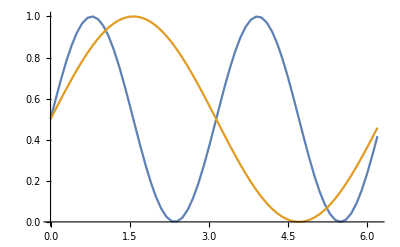

```mathematica
realRescale=Rescale[realData];
imRescale=Rescale[imData];
plotData={{xData,realRescale}ᵀ,{xData,imRescale}ᵀ};
ListPlot[plotData,Joined->True]
```

Need to now rescale the axes.

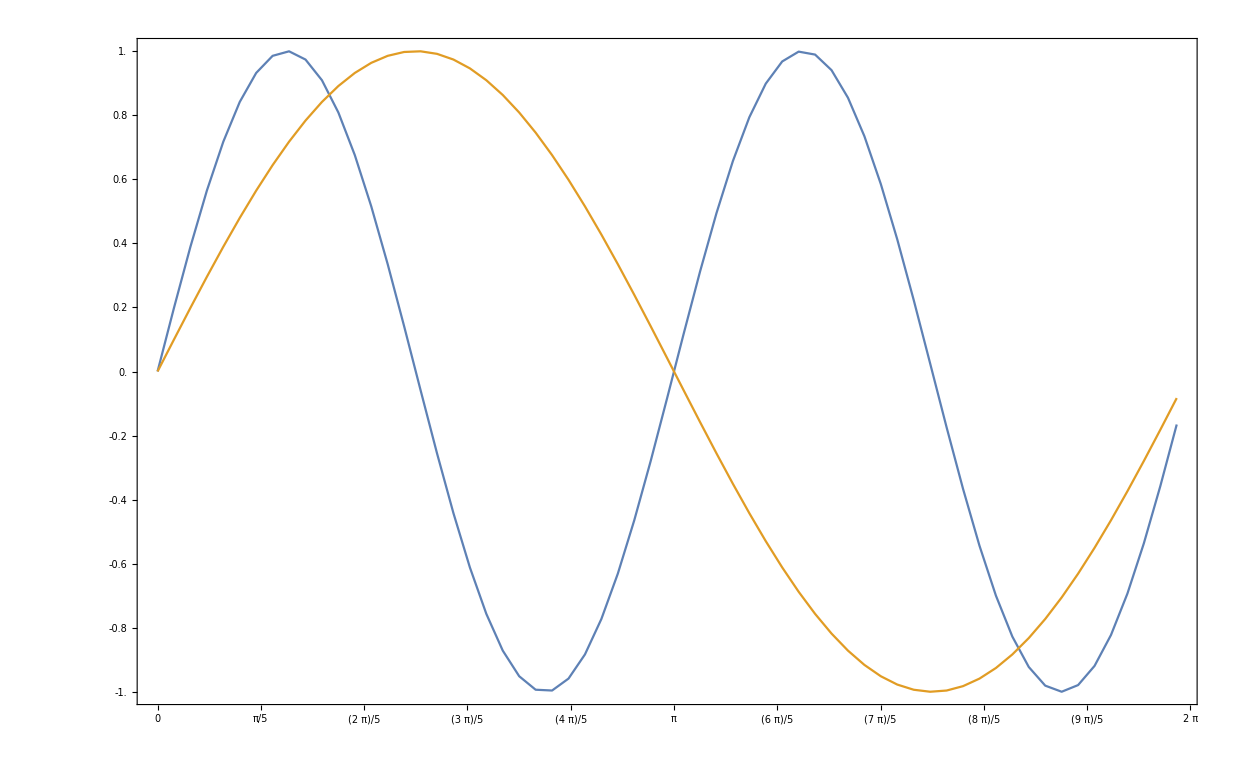

```mathematica
reMin=Min[realData];
reMax=Max[realData];
imMin=Min[imData];
imMax=Max[imData];

dT=0.1;
reTicks=Round[Table[{i,i(reMax-reMin)+reMin},{i,0,1,dT}],0.1];
imTicks=Round[Table[{i,i(imMax-imMin)+imMin},{i,0,1,dT}],0.001];
xTick=(2π)/10(Range[11]-1);
ListPlot[plotData,Joined->True,Frame->True,FrameTicks->{{reTicks,imTicks},{xTick,True}},DataRange->{0,2π}]
```